## Bayesian Statistics, Some Interesting Problems Before Exam 2 — SOLUTIONS

## Friday, Nov. 8, 2024

## 1. Best Fit Using Least Squares — Sewage Outflow Event

You have good evidence that the fecal bacteria concentration, c(d), where d is the day number, obeys the relationship, 

(c(d)=a (1/2))^d

Your civil engineers and environmental scientists measured the following concentrations (oops, I see I left the words “error bars” in the problem statement even though I decided not to deal with goodness of fit until Problem 2).

```mathematica
TableForm[{{1, 47},{2, 25},{3, 7}}]
```

1 | 47
2 | 25
3 | 7

In class we convinced ourselves, using the exact same least-squares minimization tricks that we used to derive the linear regression formula, that the best fit formula for the parameter, a, is:

a=(∑_(i=1)^3 (1/2)^i f_i)/(∑_(i=1)^3 (1/2)^(2i))

With the numbers above, this is

```mathematica
a=(47/2+25/4+7/8)/(1/4+1/16+1/64); N[a]
```

93.3333

## 2. More Sewage — Poisson Statistics and χ^2

Bacteria concentrations are obtained by your environmental scientists as follows:

They take a liter of water from the the ocean. They mix a nutrient into the water. They pour it into a large shallow dish, warm the water to 100 .baF, and wait six hours.

Then they visually count the number of bacterial colonies in the sample. This is called a “fecal coliform count.”

Given that the procedure is counting a fundamentally discrete quantity (the coliforms), and that these have an overall rate, and that in a given sample, the presence or absence of counts is randomly distributed, we would expect Poisson statistics.

It is certainly the case that 

σ_1^2=47

is a fine way to get σ_1, and I had not thought of that, and I am glad people mentioned it. I was thinking of a slightly better way, given that we have a fit to three days of data, which is to use the results of the best fit when computing variances. The predicted counts for Day 1, Day 2, and Day 3 are a/2, a/4, and a/8, respectively.

Using those predictions, our best estimate of the variances is

σ_1^2=a/2

σ_2^2=a/4

σ_3^2=a/8

where a=93.33 is what we got in Problem 1.

So our χ^2 is

```mathematica
chisquared=(47-a/2)^2/(a/2)+(25-a/4)^2/(a/4)+(7-a/8)^2/(a/8);N[chisquared]
```

1.9881

There are 3 data points, and 1 parameter to fit them. Therefore the expected χ^2 was 3-1=2. So 1.98 is exactly in line with what we would expect.

Note that not only does real-world data fluctuate, but χ^2can fluctuate from sample to sample, and so even if we had gotten any χ^2 between about 1 and 3, I would not have had any issues with the data.

## 3. Hamilton vs. Madison — Done Better

We know that the analysis we did of the Hamilton vs. Madison authorship is very sensitive to the data binning. Let’s do it better!

Use the tabulated data for Hamilton and Madison to get rates of upon per thousand words for each author:

```mathematica
aHamilton =1/1000(0 * 0+1*0.5 + 10*1.5 + 11*2.5 + 11*3.5+10*4.5 + 3 * 5.5 + 1 * 6.5 + 1 * 7.5)/48
```

0.00327083

```mathematica
aMadison =1/1000(41 * 0+7*0.5 + 2*1.5 + 0*2.5 + 0*3.5+0*4.5 + 0 * 5.5 +0 * 6.5 + 0 * 7.5)/50
```

0.00013

These values of a_Hamilton and a_Madison are now rates of “upon” per word (because I put in the factor of 1000). Before I leave the data table too far behind, I should also define the priors:

```mathematica
priorHamilton=48/98;
priorMadison=50/98;
```

Now I am going to multiply by 2008 to get the average of (the expected number of) “upon”s:

```mathematica
expectedHamilton=aHamilton*2008
```

6.56783

```mathematica
expectedMadison=aMadison*2008
```

0.26104

These are just expectations. The fact is that 2 were seen. So now we need to use these expectations to get the likelihood that 2 were seen. For Hamilton that is:

```mathematica
likelihoodOf2Hamilton=(expectedHamilton)^2/Factorial[2] Exp[-expectedHamilton]
```

0.0302998

For Madison, the likelihood is:

```mathematica
likelihoodOf2Madison=(expectedMadison)^2/Factorial[2] Exp[-expectedMadison]
```

0.0262431

Holy smokes! This result quite surprises me because they are so similar, but for different reasons! In the case of Hamilton, 2 is an unusually small number of “upon”s for a 2008-word essay. In the case of Madison, 2 is an unusually large number of “upon”s for a 2008-word essay.

Well, despite the surprise in the likelihoods, let’s finish the calculation and get the posteriors:

```mathematica
posteriorHamilton = (likelihoodOf2Hamilton * priorHamilton)/(likelihoodOf2Hamilton * priorHamilton+likelihoodOf2Madison * priorMadison)
```

0.525706

```mathematica
posteriorMadison = (likelihoodOf2Madison * priorMadison)/(likelihoodOf2Hamilton * priorHamilton+likelihoodOf2Madison * priorMadison)
```

0.474294

I’d say this word-counting game has next-to-no predictive value at all for this particular essay.

NB: The very critical of you might say this is not a Poisson statistics problem, and indeed it isn’t. There weren’t an infinite number of trials each with infinitesimal probability of yielding an “upon”; there were 2008 trials each with a very small probability of yielding an “upon.” So this is a binomial distribution and the proper way to calculate the likelihood for Hamilton would be:

(2008
2)*aHamilton^2*(1-aHamilton)^2006

And for Madison it would be:

(2008
2)*aMadison^2*(1-aMadison)^2006

The bottom line is, I agree with you, and perhaps we ought to do it that way, and see how much these slightly more accurate likelihoods change the final answer. It will be negligible.

If there is time on the review night, we can review Young together and try to do this slightly more accurate approach. The tricky thing, and the reason I didn’t do it this way is because raising a number just slightly less than 1 to the 2006 power is fraught with opportunity for loss-of-precision errors.

I frankly don’t know how to do it exactly, and doing it approximately is going to amount to doing the exact same approximations as Young used to derive the Poisson distribution. If we tackle this, we should begin by reviewing the derivation on Young p. 59.

## 4. Gaussian Data with a Gaussian Prior

We have been doing introductory problems where the prior was a flat line for some range. That made it easy to tabulate the prior. In the real world, this might have to be done, but more commonly the prior belief is captured in a more complex function.

Suppose, after studying past data, you come to the conclusion that a good prior for bacteria survival time is:

```mathematica
prior[m_]:=1/(√(2Pi))Exp[-(m-5)^2/2]
```

In other words the survival time is most likely 5 hours, but it has a standard deviation of 1.

Along comes three new data points for the survival time, x=3.6, x=4.7, and x=5.8 hours.

(a) If you knew m (you don’t! you only have its prior!), what is the likelihood of getting x=3.6? Your answer will be a function of m.

```mathematica
likelihood1[m_]:=1/(√(2Pi))Exp[-(3.6-m)^2/2]
```

Of course there is the blather about how I should be carrying along a Δx in the likelihoods, but I’ll point out the step where that would cease to matter.

(b) Repeat for x=4.7.

```mathematica
likelihood2[m_]:=1/(√(2Pi))Exp[-(4.7-m)^2/2]
```

(c) Repeat for x=5.8.

```mathematica
likelihood3[m_]:=1/(√(2Pi))Exp[-(5.8-m)^2/2]
```

(d) What is the joint likelihood (the product of these three functions)? Again this will be a function of m.

```mathematica
jointLikelihood[m_]:=likelihood1[m]*likelihood2[m]*likelihood3[m]
```

(e) What is the product of these three functions multiplied by the prior?

```mathematica
product[m_]:=jointLikelihood[m]*prior[m]
```

(f) Now I will throw Mathematica at this thing and graph it and compute its integral too. The integral will be the denominator in our final expression for the posterior, which is a new function of m.

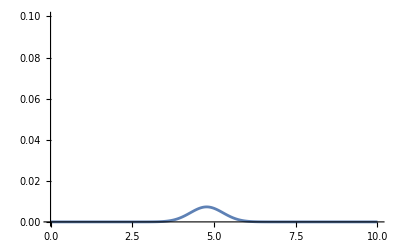

```mathematica
Plot[product[m],{m, 0, 10}, PlotRange->{{0,10},{0,0.1}}]
```

That looks like it could be a very low Gaussian.

Now something dawns on us: the product of four Gaussians is a Gaussian! It has to be! The product of exponentials is an exponential because exponents add. The exponents were quadratic functions of m. The sum of a bunch of quadratic functions is a quadratic function.

Of course, this Gaussian isn’t normalized, because the likelihoods aren’t normalized. But we aren’t done. We have to compute its integral and stick that in the denominator of Bayes theorem.

```mathematica
denominator=NIntegrate[product[m],{m,-Infinity,Infinity}]
```

0.00915264

Now that we have the integral that goes in the denominator, we can finally compute and graph the posterior:

```mathematica
posterior[m_]:=product[m]/denominator
```

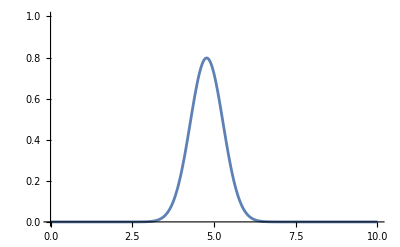

```mathematica
Plot[posterior[m],{m, 0, 10}, PlotRange->{{0,10},{0,1}}]
```

That is very interesting. How does it compare to our prior?

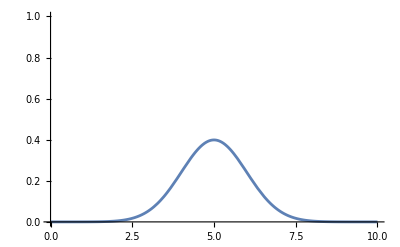

```mathematica
Plot[prior[m],{m, 0, 10}, PlotRange->{{0,10},{0,1}}]
```

So our three new data points have not changed the center of our Gaussian very much, but they have narrowed it compared to our broad prior. We have more certainty now about this bacteria’s survival time.